```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

# Neural Logic Networks

Working repo: https://github.com/github/neural-logic

## A classification problem

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

### Feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],Sequence@@Normal[Drop[Normal[encoders],-1]]
];
```

## A standard neural network

### Define net

```mathematica
standardNet=NetChain[{LinearLayer[20,"Input"->inputSize],ElementwiseLayer["ScaledExponentialLinearUnit"],LinearLayer[4],SoftmaxLayer[]}];
```

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->standardNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->CrossEntropyLossLayer["Probabilities"]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

```mathematica
NetFlatten[trainableNet]
```

NetGraph[<>]

### Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"];
```

```mathematica
result
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:11900  rounds:476  time:34s  examples/s:22609
data | ,,  training examples:1555  validation examples:173  processed examples:761600  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-3  error:0%
validation | ,,  loss:1.99×10^-2  error:0.578%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
trainedNet=NetGraph[
<|"TrainedNet"->NetDelete[result["TrainedNet"],"Loss"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]
```

NetGraph[<>]

### Evaluate

```mathematica
predictions=Association[{"Prediction"->trainedNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval=HardNetClassifyEvaluation[predictions];
eval["Accuracy"]
```

0.99422

```mathematica
weights=Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedNet],{All,"Weights"}]]]]];
```

```mathematica
standardNetSize=Quantity[Length[weights]*32/1024.0,"Kilobytes"]
```

15.625 kB

## A neural logic network

### Define neural logic net

```mathematica
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,64],
HardNeuralNOT[64,Length[classes]]
}];
```

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

```mathematica
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
```

```mathematica
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
```

### Train net

```mathematica
result=NetTrain[trainableNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity];
```

```mathematica
result
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:11375  rounds:455  time:39s  examples/s:18710
data | ,,  training examples:1555  validation examples:173  processed examples:728000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.24×10^-2  error:1.19%
validation | ,,  loss:1.84×10^-2  error:0.578%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

### Examine trained net

```mathematica
hnf=HardNetFunction[hardNet,result["TrainedNet"]];
```

```mathematica
hnbe=HardNetBooleanExpression[hnf,inputSize]
```

{{b1||b4||b5||b6||b7,b1||b4||b15||b16||b19,b1||b3||b5||b7||b8||b15||b19,!(b2||b10||b17||b20),!(b9||b10||b14||b16||b17||b20),b1||b4||b6||b11||b15||b19,!(b1||b16||b21),!(b1||b3||b4||b5||b21),!(b4||b5||b6||b7||b21),b1||b7||b8||b15||b16||b19,b5||b11||b15||b19,!(b1||b4||b5||b18||b21),b2||b11||b15||b19,b1||b15||b19,!b20,!(b2||b9||b11||b14||b17),b1||b4||b15||b16||b19,b1||b2||b4||b8||b15||b19,b1||b4||b5||b6||b15||b16||b19,b1||b2||b5||b8||b15||b16||b19,!(b2||b17||b20),b4||b6||b15||b16||b19||b20,b1||b4||b5||b9||b10||b15||b17||b19,b5||b6||b12||b14||b15||b19,b2||b3||b5||b15||b19||b21,b4||b5||b6||b9||b15||b18||b19,b1||b5||b11||b15||b19,!(b9||b10||b12||b13||b17),!(b4||b5||b11||b16||b21),!(b1||b4||b5||b18||b21),b5||b6||b11||b12||b15||b16||b19,!(b11||b18||b20),b1||b4||b7||b8||b15||b19||b21,b1||b4||b5||b6||b16||b19,b1||b2||b4||b6||b7||b15||b19,b4||b5||b6||b15||b19,b1||b5||b11||b13||b15||b17||b19,!(b9||b17||b20),b5||b15||b16||b19,!(b3||b6||b17||b20),b1||b5||b14||b15||b18||b19||b21,b4||b5||b6||b15||b17||b19||b21,b1||b4||b5||b11||b15||b16||b19||b21,!(b2||b8),b1||b4||b5||b6||b11||b15||b16||b19||b20,b1||b4||b7||b8||b15||b19||b21,b1||b4||b5||b6||b15||b16||b18||b19||b20,b1||b4||b15||b16||b19||b21,b4||b6||b11||b15||b19,b1||b4||b6||b9||b10||b14||b15||b17||b21,b1||b4||b12||b14||b15||b19,!(b9||b10||b12||b13||b17||b18),!(b9||b10||b14||b16||b17||b20),b4||b5||b6||b9||b10||b15||b17||b19||b21,b5||b6||b15||b16||b19,!(b2||b7||b8),b5||b11||b15||b17||b18||b19||b21,!(b1||b3||b6||b8),!(b2||b3||b18),!(b13||b14),b1||b5||b11||b15||b19,!(b8||b9||b10||b17||b20),!(b9||b13||b17||b18),b1||b13||b15||b16||b19},{b1||b4||b5||b6||b7,!(b1||b4||b15||b16||b19),!(b1||b3||b5||b7||b8||b15||b19),b2||b10||b17||b20,b9||b10||b14||b16||b17||b20,!(b1||b4||b6||b11||b15||b19),b1||b16||b21,b1||b3||b4||b5||b21,b4||b5||b6||b7||b21,!(b1||b7||b8||b15||b16||b19),!(b5||b11||b15||b19),b1||b4||b5||b18||b21,!(b2||b11||b15||b19),!(b1||b15||b19),!b20,b2||b9||b11||b14||b17,b1||b4||b15||b16||b19,!(b1||b2||b4||b8||b15||b19),b1||b4||b5||b6||b15||b16||b19,!(b1||b2||b5||b8||b15||b16||b19),b2||b17||b20,!(b4||b6||b15||b16||b19||b20),!(b1||b4||b5||b9||b10||b15||b17||b19),b5||b6||b12||b14||b15||b19,!(b2||b3||b5||b15||b19||b21),b4||b5||b6||b9||b15||b18||b19,!(b1||b5||b11||b15||b19),b9||b10||b12||b13||b17,b4||b5||b11||b16||b21,b1||b4||b5||b18||b21,!(b5||b6||b11||b12||b15||b16||b19),b11||b18||b20,!(b1||b4||b7||b8||b15||b19||b21),b1||b4||b5||b6||b16||b19,b1||b2||b4||b6||b7||b15||b19,!(b4||b5||b6||b15||b19),b1||b5||b11||b13||b15||b17||b19,!(b9||b17||b20),!(b5||b15||b16||b19),b3||b6||b17||b20,!(b1||b5||b14||b15||b18||b19||b21),b4||b5||b6||b15||b17||b19||b21,b1||b4||b5||b11||b15||b16||b19||b21,b2||b8,b1||b4||b5||b6||b11||b15||b16||b19||b20,!(b1||b4||b7||b8||b15||b19||b21),b1||b4||b5||b6||b15||b16||b18||b19||b20,b1||b4||b15||b16||b19||b21,!(b4||b6||b11||b15||b19),b1||b4||b6||b9||b10||b14||b15||b17||b21,!(b1||b4||b12||b14||b15||b19),b9||b10||b12||b13||b17||b18,b9||b10||b14||b16||b17||b20,!(b4||b5||b6||b9||b10||b15||b17||b19||b21),!(b5||b6||b15||b16||b19),b2||b7||b8,!(b5||b11||b15||b17||b18||b19||b21),b1||b3||b6||b8,b2||b3||b18,b13||b14,!(b1||b5||b11||b15||b19),b8||b9||b10||b17||b20,b9||b13||b17||b18,b1||b13||b15||b16||b19},{!(b1||b4||b5||b6||b7),!(b1||b4||b15||b16||b19),!(b1||b3||b5||b7||b8||b15||b19),b2||b10||b17||b20,b9||b10||b14||b16||b17||b20,!(b1||b4||b6||b11||b15||b19),!(b1||b16||b21),!(b1||b3||b4||b5||b21),b4||b5||b6||b7||b21,!(b1||b7||b8||b15||b16||b19),!(b5||b11||b15||b19),!(b1||b4||b5||b18||b21),b2||b11||b15||b19,!(b1||b15||b19),b20,b2||b9||b11||b14||b17,!(b1||b4||b15||b16||b19),b1||b2||b4||b8||b15||b19,!(b1||b4||b5||b6||b15||b16||b19),!(b1||b2||b5||b8||b15||b16||b19),b2||b17||b20,b4||b6||b15||b16||b19||b20,b1||b4||b5||b9||b10||b15||b17||b19,!(b5||b6||b12||b14||b15||b19),b2||b3||b5||b15||b19||b21,!(b4||b5||b6||b9||b15||b18||b19),!(b1||b5||b11||b15||b19),b9||b10||b12||b13||b17,!(b4||b5||b11||b16||b21),!(b1||b4||b5||b18||b21),!(b5||b6||b11||b12||b15||b16||b19),b11||b18||b20,b1||b4||b7||b8||b15||b19||b21,!(b1||b4||b5||b6||b16||b19),!(b1||b2||b4||b6||b7||b15||b19),!(b4||b5||b6||b15||b19),!(b1||b5||b11||b13||b15||b17||b19),b9||b17||b20,!(b5||b15||b16||b19),b3||b6||b17||b20,!(b1||b5||b14||b15||b18||b19||b21),b4||b5||b6||b15||b17||b19||b21,!(b1||b4||b5||b11||b15||b16||b19||b21),b2||b8,b1||b4||b5||b6||b11||b15||b16||b19||b20,b1||b4||b7||b8||b15||b19||b21,!(b1||b4||b5||b6||b15||b16||b18||b19||b20),!(b1||b4||b15||b16||b19||b21),!(b4||b6||b11||b15||b19),b1||b4||b6||b9||b10||b14||b15||b17||b21,!(b1||b4||b12||b14||b15||b19),!(b9||b10||b12||b13||b17||b18),b9||b10||b14||b16||b17||b20,b4||b5||b6||b9||b10||b15||b17||b19||b21,!(b5||b6||b15||b16||b19),b2||b7||b8,b5||b11||b15||b17||b18||b19||b21,b1||b3||b6||b8,b2||b3||b18,!(b13||b14),!(b1||b5||b11||b15||b19),b8||b9||b10||b17||b20,b9||b13||b17||b18,!(b1||b13||b15||b16||b19)},{!(b1||b4||b5||b6||b7),!(b1||b4||b15||b16||b19),!(b1||b3||b5||b7||b8||b15||b19),b2||b10||b17||b20,b9||b10||b14||b16||b17||b20,!(b1||b4||b6||b11||b15||b19),b1||b16||b21,!(b1||b3||b4||b5||b21),!(b4||b5||b6||b7||b21),b1||b7||b8||b15||b16||b19,!(b5||b11||b15||b19),!(b1||b4||b5||b18||b21),b2||b11||b15||b19,!(b1||b15||b19),b20,b2||b9||b11||b14||b17,!(b1||b4||b15||b16||b19),b1||b2||b4||b8||b15||b19,!(b1||b4||b5||b6||b15||b16||b19),b1||b2||b5||b8||b15||b16||b19,b2||b17||b20,!(b4||b6||b15||b16||b19||b20),b1||b4||b5||b9||b10||b15||b17||b19,!(b5||b6||b12||b14||b15||b19),b2||b3||b5||b15||b19||b21,!(b4||b5||b6||b9||b15||b18||b19),!(b1||b5||b11||b15||b19),b9||b10||b12||b13||b17,b4||b5||b11||b16||b21,b1||b4||b5||b18||b21,!(b5||b6||b11||b12||b15||b16||b19),b11||b18||b20,b1||b4||b7||b8||b15||b19||b21,!(b1||b4||b5||b6||b16||b19),!(b1||b2||b4||b6||b7||b15||b19),!(b4||b5||b6||b15||b19),!(b1||b5||b11||b13||b15||b17||b19),b9||b17||b20,!(b5||b15||b16||b19),b3||b6||b17||b20,!(b1||b5||b14||b15||b18||b19||b21),!(b4||b5||b6||b15||b17||b19||b21),b1||b4||b5||b11||b15||b16||b19||b21,b2||b8,!(b1||b4||b5||b6||b11||b15||b16||b19||b20),b1||b4||b7||b8||b15||b19||b21,!(b1||b4||b5||b6||b15||b16||b18||b19||b20),b1||b4||b15||b16||b19||b21,!(b4||b6||b11||b15||b19),!(b1||b4||b6||b9||b10||b14||b15||b17||b21),!(b1||b4||b12||b14||b15||b19),b9||b10||b12||b13||b17||b18,b9||b10||b14||b16||b17||b20,!(b4||b5||b6||b9||b10||b15||b17||b19||b21),!(b5||b6||b15||b16||b19),!(b2||b7||b8),!(b5||b11||b15||b17||b18||b19||b21),!(b1||b3||b6||b8),b2||b3||b18,b13||b14,!(b1||b5||b11||b15||b19),b8||b9||b10||b17||b20,b9||b13||b17||b18,!(b1||b13||b15||b16||b19)}}

### Evaluate

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[encoders["Acceptability"]],featureLayer[KeyDrop[#,"Acceptability"]]&,#["Acceptability"]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

1.

```mathematica
netSize=Quantity[Length[Flatten[ExtractWeights[result["TrainedNet"]]]]/8/1024//N,"Kilobytes"]
```

0.195313 kB

```mathematica
standardNetSize/netSize
```

80.

## Notes

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

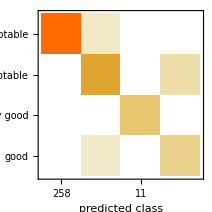
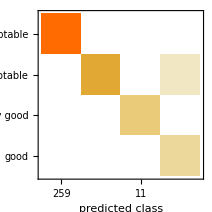
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.80.6) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.973 ± 0.013
Mean cross entropy | 0.0273 ± 0.014
Single evaluation time | 6.86 ms/example
Batch evaluation speed | 1.34 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.40.4) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.974 ± 0.014
Mean cross entropy | 0.026 ± 0.015
Single evaluation time | 7.02 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,trainedHardNet}
```

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.99422